```mathematica
data:=Import["fatal-police-shootings-data.csv"]
```

```mathematica
allDates := data[[2;;, 3]]
dates:=Select[allDates,StringFreeQ[#,"2019"]&]
```

```mathematica
allDates:=data[[2;;, 3]]
dates:=Select[allDates,StringStartsQ[#,{"2015","2016","2017","2018"}]&]
```

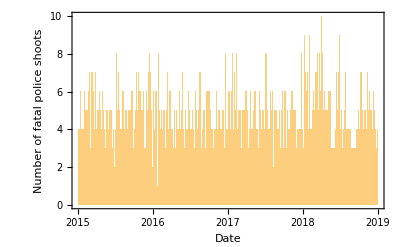
-Graphics-Number of fatal police shoots each day in the USA between 2015-01-01 to 2018-12-31.

```mathematica
Labeled[DateHistogram[
dates,"Day",
Frame->{True,True,True,True},
Ticks->{{"2015","2016","2017","2018","2019"},None},
FrameTicks->{Automatic,Range[0,Max[Counts[dates]]]},
FrameLabel->{"Date","Number of fatal police shoots"}
],Style["Number of fatal police shoots each day in the USA between 2015-01-01 to 2018-12-31.","Graphics"]]
```

{2015-02-28,2016-02-28,2016-02-28,2016-02-29,2016-02-29,2016-02-29,2016-02-29,2016-03-01,2016-03-01,2016-03-01}

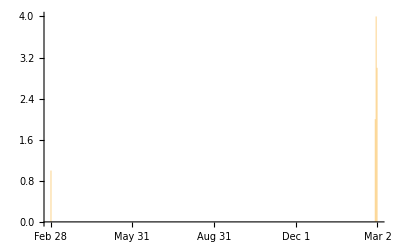

```mathematica
tempDates={"2015-02-28","2016-02-28","2016-02-28","2016-02-29","2016-02-29","2016-02-29","2016-02-29","2016-03-01","2016-03-01","2016-03-01"}
DateHistogram[tempDates,"Day"]
```